```mathematica
Δ=1
ϵ=0.5*Δ
ωc=0.05*Δ 
β=0.95 /Δ
α= 0.1 *Δ/Pi
γ=100*Δ
Ω=γ*ωc 
gscuare=Ω*α /4
```

1

0.5

0.05

0.95

0.031831

100

5.

0.0397887

```mathematica
J[w_]:=(α*w* ωc)/(w^2+(w^4 *ωc^2)/Ω^4+ωc^2)
J2[w_]:=(α*w* ωc)/(w^2+ωc^2)
```

```mathematica
J[-w_]:=-J[w]
J2[-w_]:=-J2[w]
```

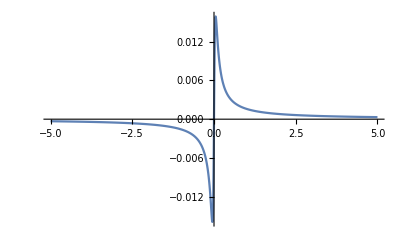

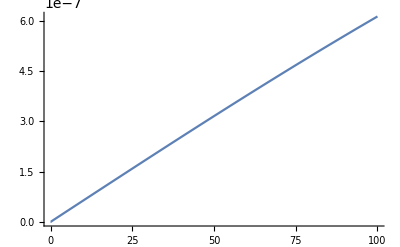

```mathematica
Plot[J[w],{w,-5,5}, PlotRange->All]
Plot[J2[w]-J[w],{w,0,100}, PlotRange->All]
```

```mathematica
omega02= Integrate[w*J[w],{w,0,Infinity}]/Integrate[J[w]/w,{w,0,Infinity}]
omega022= Integrate[w*J2[w],{w,0,Infinity}]/Integrate[J2[w]/w,{w,0,Infinity}]
```

25.+0. ⅈ

Integrate::idiv: Integral of (0.00159155 w^2)/(0.0025+w^2) does not converge on {0,∞}.

20. ∫_0^∞ (0.00159155 w^2)/(0.0025+w^2)ⅆw

```mathematica
g2=1/(2Pi Sqrt[ omega02])Integrate[w*J[w],{w,0,Infinity}]
```

0.0397848+0. ⅈ

```mathematica
J1[w_]:= (4 g2 J2[w])/((1/Pi Integrate[J2[x]/(w-x), {x, -Infinity, Infinity}, PrincipalValue->True])^2+ (J2[w])^2)
```

```mathematica
J1[w]
```

ConditionalExpression[((0.000253278+0. ⅈ) w)/((0.0025+w^2) ((2.53303×10^-6 w^2)/((0.0025+w^2)^2)+(6.33257×10^-9)/((0.0025+1. w^2)^2))),w∈ℝ]

```mathematica
((0.00016016282206531224+0. ⅈ) w)/((0.0025000000000000005+w^2) ((2.533029591058445*^-6 w^2)/((0.0025000000000000005+w^2)^2)+(6.332573977646114*^-9)/((0.0025000000000000005+1. w^2)^2)))
```

((0.000160163+0. ⅈ) w)/((0.0025+w^2) ((2.53303×10^-6 w^2)/((0.0025+w^2)^2)+(6.33257×10^-9)/((0.0025+1. w^2)^2)))

```mathematica
Simplify[((0.0002532776326088451+0. ⅈ) w)/((0.0025000000000000005+w^2) ((2.533029591058445*^-6 w^2)/((0.0025000000000000005+w^2)^2)+(6.332573977646114*^-9)/((0.0025000000000000005+1. w^2)^2)))]
```

((99.99+0. ⅈ) w (0.0025+w^2))/(0.0025+1. w^2)

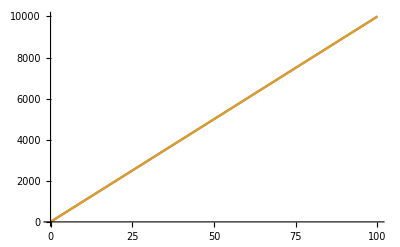

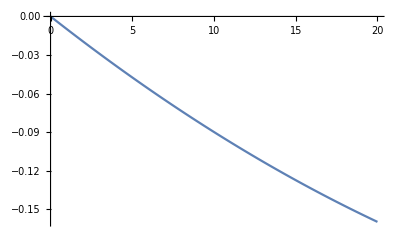

```mathematica
Plot[{((99.99000149975001+0. ⅈ) w (0.0025000000000000005+w^2))/(0.002500000000000001+1. w^2), γ*w Exp[-w/1000000]},{w,0,100}]
Plot[{((99.99000149975001+0. ⅈ) w (0.0025000000000000005+w^2))/(0.002500000000000001+1. w^2)- γ*w Exp[-w/1000000]},{w,0,20}]
```

```mathematica
J1[w_]:=((99.99000149975001+0. ⅈ) w (0.0025000000000000005+w^2))/(0.002500000000000001+1. w^2)
```

```mathematica
1/(2Pi)Integrate[J1[w]/w,{w,0,Infinity}]
```

Integrate::idiv: Integral of (0.249975+0. ⅈ)/(0.0025+1. w^2)+((«18»+0. ⅈ) w^2)/(«21»+1. w^2) does not converge on {0,∞}.

(∫_0^∞ ((99.99+0. ⅈ) (0.0025+w^2))/(0.0025+1. w^2)ⅆw)/(2 π)

```mathematica
J1[√omega02]
```

499.95+0. ⅈ

```mathematica
nb[w_]:=1/(Exp[β*w]-1)
```

```mathematica
nb[√omega02]
```

0.0087272+0. ⅈ

```mathematica
gamma=J1[√omega02]*(1+nb[√omega02])
```

504.313+0. ⅈ

```mathematica
gammabar=J1[√omega02]*nb[√omega02]
```

4.36316+0. ⅈ